```mathematica
(*Defining parameters*)
A0=100;
B0:=0.04;
h0:=2.3;
basal0:=0.1;
A1:=300;(*Modified from 184*)
B1:=0.07;(*Modified from 0.007*)
h1:=0.45;(*Modified from 0.89*)
basal1:=1.98;
A2:=57.6;
B2:=160;
h2:=3.7;
basal2:=0.52;
Aa:=0.9;
Ba:=0.072;
ha:=1.9;
basala:=0.105;
b0:=10;
b1:=43;
b2:=6;
etaN:=0;
etaG:=0.652;

Np:=1;
kr:=1/5;(*Minutes or seconds?*)
k:=b0*kr;
g:=1/30;(*Minutes or seconds*)
(*Define transfer functions*)
f0[IPTG_]:=A0/(1+(IPTG/B0)^h0)+basal0;
f1[y0A_]:=A1/(1+(y0A/B1)^h1)+basal1;
f2[y1A_]:=A2/(1+(y1A/B2)^h2)+basal2;
fa[ATC_]:=Aa/(1+(ATC/Ba)^ha)+basala;
(*Define steady state values, log gains and noises*)
```

```mathematica
y0s:=k/g;
y0As[IPTG_]:=f0[IPTG]*y0s;
y1s[IPTG_]:=(Np*f1[y0As[IPTG]])/g;
y2s[IPTG_]:=(Np*f2[y1s[IPTG]])/g;
eta2int0:=(b0+1)/y0s;
eta2int1[IPTG_]:=(b1+1)/y1s[IPTG];
eta2int2[IPTG_]:=(b2+1)/y2s[IPTG];
eta2int3:=0;
H10[IPTG_]:=h1/(A1*f1[y0As[IPTG]])*(f1[y0As[IPTG]]-basal1)*(basal1+A1-f1[y0As[IPTG]]);
H21[IPTG_]:=h2/(A2*f2[y1s[IPTG]])*(f2[y1s[IPTG]]-basal2)*(basal2+A2-f2[y1s[IPTG]]);
eta20:=eta2int0+etaG^2;
eta21[IPTG_]:=eta2int1[IPTG]+1/2*(H10[IPTG])^2*eta20+1/2 etaN^2+etaG^2*(1-H10[IPTG]);
eta22[IPTG_]:=eta2int2[IPTG]+1/2*(H21[IPTG])^2*eta21[IPTG]+1/8*(H21[IPTG])^2*(H10[IPTG])^2*eta20+etaN^2*(1/2+1/8*(H21[IPTG])^2-3/4*H21[IPTG])+etaG^2*(1-H21[IPTG]-1/4*(H21[IPTG])^2*H10[IPTG]+1/2*H21[IPTG]*H10[IPTG]);
eta23:=etaG^2+eta2int3+1/2*etaN^2;
```

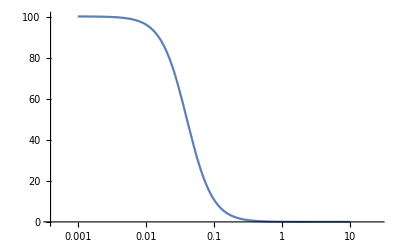

```mathematica
LogLinearPlot[f0[IPTG],{IPTG,10^-3,10}]
```

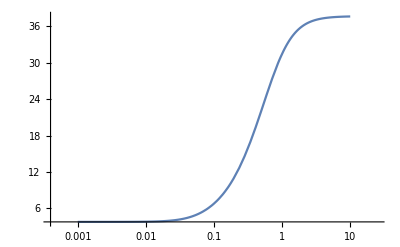

```mathematica
LogLinearPlot[f1[y0As[IPTG]],{IPTG,10^-3,10}]
```

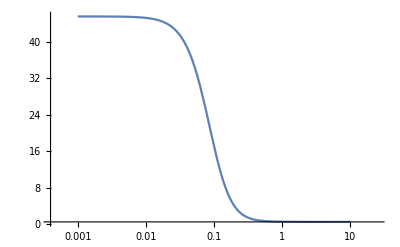

```mathematica
LogLinearPlot[f2[y1s[IPTG]],{IPTG,10^-3,10}]
```

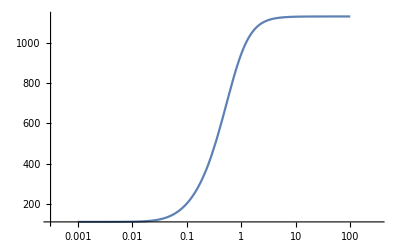

```mathematica
LogLinearPlot[y1s[IPTG],{IPTG,10^-3,100}]
```

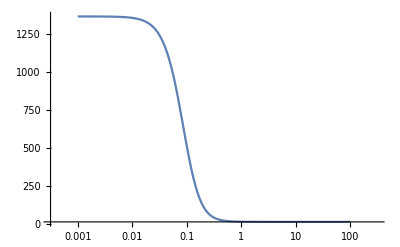

```mathematica
LogLinearPlot[y2s[IPTG],{IPTG,10^-3,100}]
```

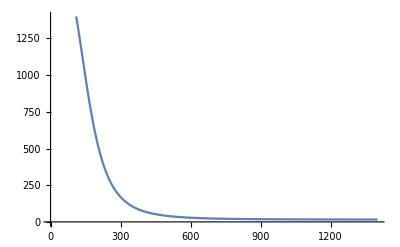

```mathematica
y2sv2[y1s_]:=(Np*f2[y1s])/g;
Plot[y2sv2[y1s],{y1s,0,1400},PlotRange->{0,1400}]
```

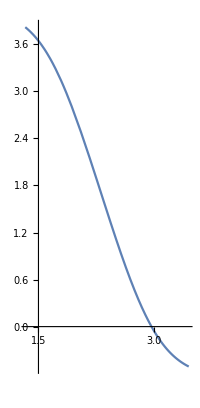

```mathematica
(*LogLinearPlot[f2[y1s[IPTG]],{IPTG,10^-3,10}]*)
ParametricPlot[{Log[f1[y0As[IPTG]]],Log[f2[y1s[IPTG]]]},{IPTG,10^-3,1}]
```

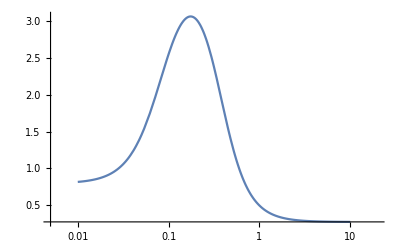

```mathematica
LogLinearPlot[H21[IPTG],{IPTG,10^-2,10}]
```

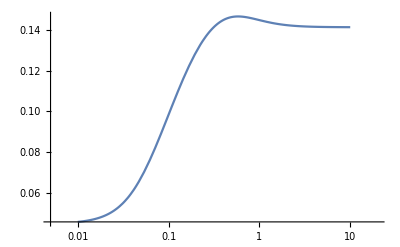

```mathematica
LogLinearPlot[(H10[IPTG])^2,{IPTG,10^-2,10}]
```

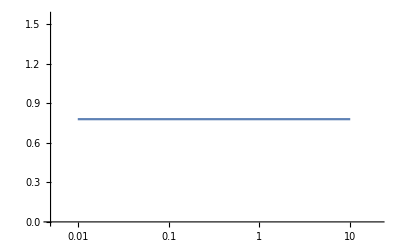

```mathematica
LogLinearPlot[Sqrt[eta20],{IPTG,10^-2,10}]
```

```mathematica
C03:=etaG^2;
C12[IPTG_]:=-1/2*H21[IPTG]*eta2int1[IPTG]-3/8*H21[IPTG]*(H10[IPTG])^2*eta2int0+etaG^2*(1-1/2*H21[IPTG]-1/2*H10[IPTG]-3/8 H21[IPTG]*(H10[IPTG])^2+3/4*H21[IPTG]*H10[IPTG])+etaN^2*(1/2-3/8*H21[IPTG]);
C13[IPTG_]:=etaG^2*(1-1/2*H10[IPTG])+1/2*etaN^2;
C23[IPTG_]:=etaG^2*(1-1/2*H21[IPTG]+1/4*H21[IPTG]*H10[IPTG])+etaN^2*(1/2-3/8*H21[IPTG]);
```

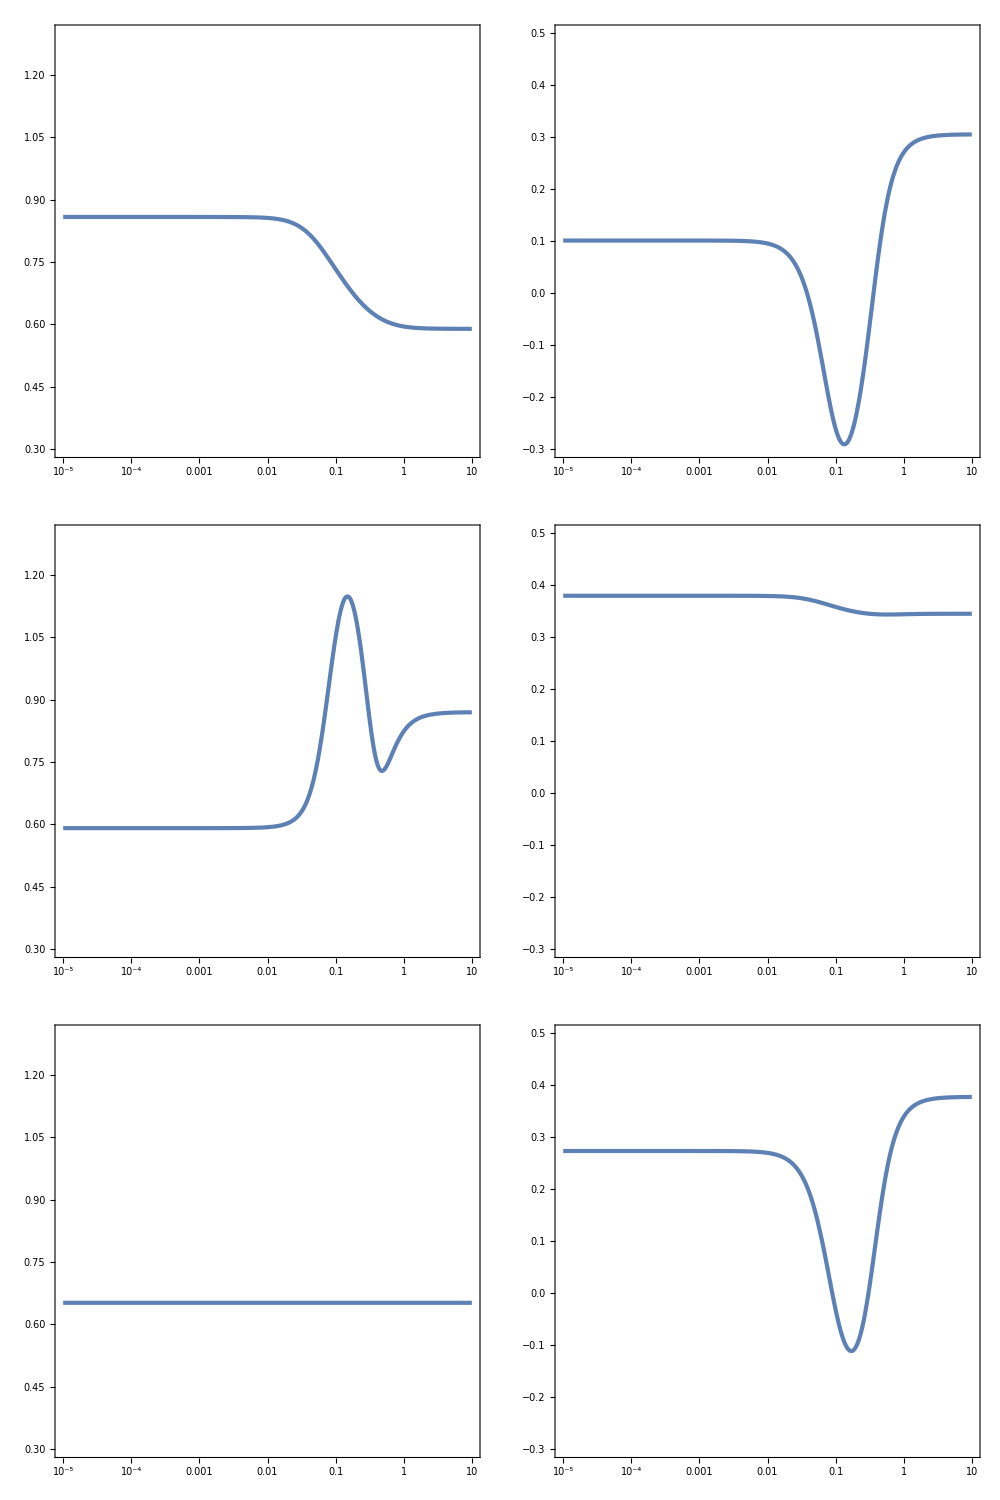

```mathematica
grapheta1=LogLinearPlot[Sqrt[eta21[IPTG]],{IPTG,10^-5,10},Frame->True,PlotRange->{{10^-5,10},{0.3,1.3}},PlotStyle->AbsoluteThickness[3],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{Automatic, Automatic}, {None, None}},AspectRatio->1,FrameStyle->Directive[Black,Thick],LabelStyle->Directive[20,FontFamily->"Palatino Linotype",Black]];

grapheta2=LogLinearPlot[Sqrt[eta22[IPTG]],{IPTG,10^-5,10},Frame->True,PlotRange->{{10^-5,10},{0.3,1.3}},PlotStyle->AbsoluteThickness[3],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{Automatic, Automatic}, {None, None}},AspectRatio->1,FrameStyle->Directive[Black,Thick],LabelStyle->Directive[20,FontFamily->"Palatino Linotype",Black]];

grapheta3=LogLinearPlot[Sqrt[eta23],{IPTG,10^-5,10},Frame->True,PlotRange->{{10^-5,10},{0.3,1.3}},PlotStyle->AbsoluteThickness[3],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{Automatic, Automatic}, {Automatic, None}},AspectRatio->1,FrameStyle->Directive[Black,Thick],LabelStyle->Directive[20,FontFamily->"Palatino Linotype",Black]];

graphc12=LogLinearPlot[C12[IPTG],{IPTG,10^-5,10},Frame->True,PlotRange->{{10^-5,10},{-0.3,0.5}},PlotStyle->AbsoluteThickness[3],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{Automatic, Automatic}, {None, None}},AspectRatio->1,FrameStyle->Directive[Black,Thick],LabelStyle->Directive[20,FontFamily->"Palatino Linotype",Black]];

graphc13=LogLinearPlot[C13[IPTG],{IPTG,10^-5,10},Frame->True,PlotRange->{{10^-5,10},{-0.3,0.5}},PlotStyle->AbsoluteThickness[3],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{Automatic, Automatic}, {None, None}},AspectRatio->1,FrameStyle->Directive[Black,Thick],LabelStyle->Directive[20,FontFamily->"Palatino Linotype",Black]];

graphc23=LogLinearPlot[C23[IPTG],{IPTG,10^-5,10},Frame->True,PlotRange->{{10^-5,10},{-0.3,0.5}},PlotStyle->AbsoluteThickness[3],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{Automatic, Automatic}, {Automatic, None}},AspectRatio->1,FrameStyle->Directive[Black,Thick],LabelStyle->Directive[20,FontFamily->"Palatino Linotype",Black],TicksStyle->Directive[Black, Thick]];

GraphicsGrid[{{grapheta1,graphc12},{grapheta2,graphc13},{grapheta3,graphc23}},Spacings->{0,0},Frame->True,AspectRatio->Full,ImageSize->{1000,1500}]
```

```mathematica
options = {Frame->True,PlotRange->{{10^-5,10},{0.3,1.3}},PlotStyle->AbsoluteThickness[3],FrameStyle->Directive[Black,Thick],LabelStyle->Directive[30,FontFamily->"Palatino Linotype",Black],FrameLabel->{Text[Style["IPTG (mM)"]],None}};
```

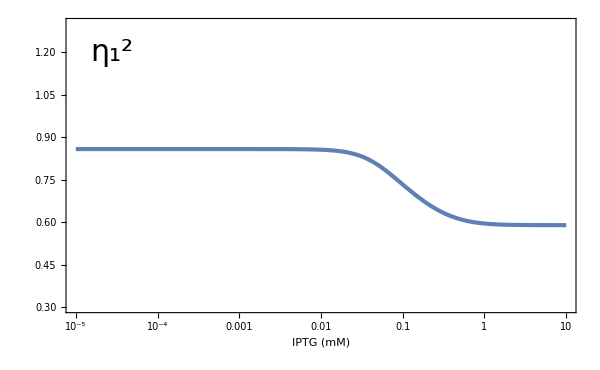

```mathematica
Show[LogLinearPlot[Sqrt[eta21[IPTG]],{IPTG,10^-5,10},Evaluate[options]],Graphics[Text[Style[ToExpression["\\eta_1^2",TeXForm,HoldForm],30,Black,FontFamily->"Palatino Linotype"],{-10.5,1.2}]],ImageSize->600]
```

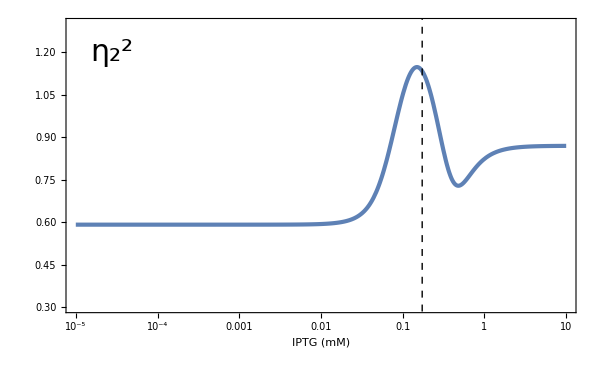

```mathematica
g111=Show[LogLinearPlot[Sqrt[eta22[IPTG]],{IPTG,10^-5,10},Evaluate[options]],Graphics[Text[Style[ToExpression["\\eta_2^2",TeXForm,HoldForm],30,Black,FontFamily->"Palatino Linotype"],{-10.5,1.2}]],ImageSize->600,Epilog->{Directive[Black,Dashed,Thick],Line[{{Log[0.173],5},{Log[0.173],-1}}]}]
```

```mathematica
Export["/home/gutiloluis/61Monograph/math/aaa.png",g111]
```

/home/gutiloluis/61Monograph/math/aaa.png

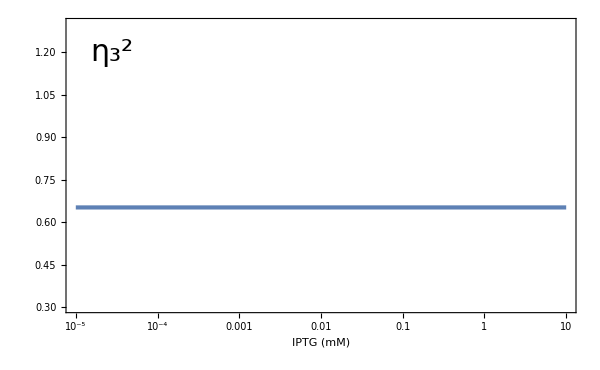

```mathematica
Show[LogLinearPlot[Sqrt[eta23],{IPTG,10^-5,10},Evaluate[options]],Graphics[Text[Style[ToExpression["\\eta_3^2",TeXForm,HoldForm],30,Black,FontFamily->"Palatino Linotype"],{-10.5,1.2}]],ImageSize->600]
```

```mathematica
options2 = {Frame->True,PlotRange->{{10^-5,10},{-0.3,0.5}},PlotStyle->AbsoluteThickness[3],FrameStyle->Directive[Black,Thick],LabelStyle->Directive[30,FontFamily->"Palatino Linotype",Black],TicksStyle->Directive[Black,Bold],FrameLabel->{Text[Style["IPTG (mM)"]],None}};
```

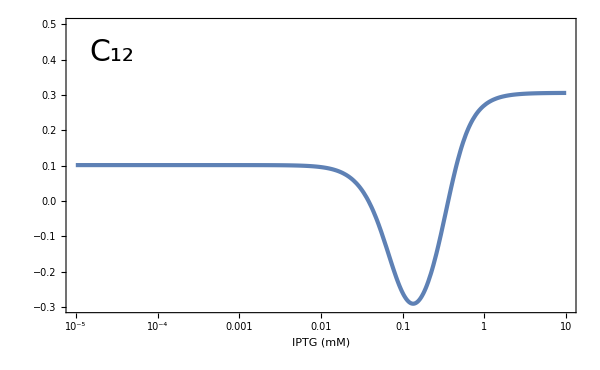

```mathematica
Show[LogLinearPlot[C12[IPTG],{IPTG,10^-5,10},Evaluate[options2]],Graphics[Text[Style[ToExpression["C_{12}",TeXForm,HoldForm],30,Black,FontFamily->"Palatino Linotype"],{-10.5,0.42}]],ImageSize->600]
```

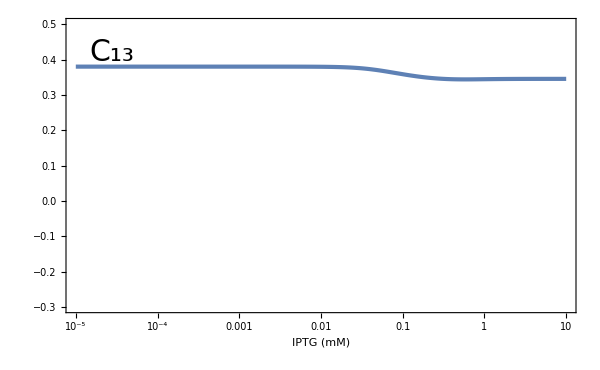

```mathematica
Show[LogLinearPlot[C13[IPTG],{IPTG,10^-5,10},Evaluate[options2]],Graphics[Text[Style[ToExpression["C_{13}",TeXForm,HoldForm],30,Black,FontFamily->"Palatino Linotype"],{-10.5,0.42}]],ImageSize->600]
```

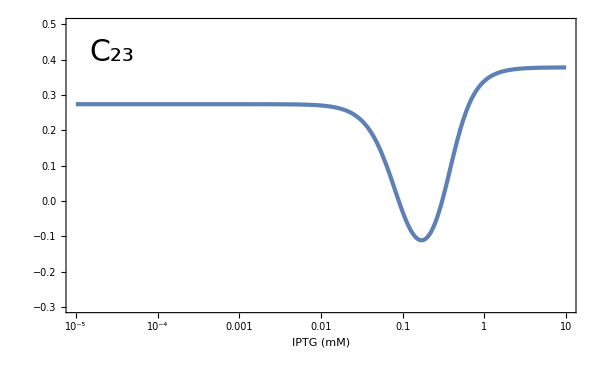

```mathematica
Show[LogLinearPlot[C23[IPTG],{IPTG,10^-5,10},Evaluate[options2]],Graphics[Text[Style[ToExpression["C_{23}",TeXForm,HoldForm],30,Black,FontFamily->"Palatino Linotype"],{-10.5,0.42}]],ImageSize->600]
```

```mathematica
(*All noise sources*)
eta22[IPTG_]:=eta2int2[IPTG]+1/2*(H21[IPTG])^2*eta21[IPTG]+1/8*(H21[IPTG])^2*(H10[IPTG])^2*eta20+etaN^2*(1/2+1/8*(H21[IPTG])^2-3/4*H21[IPTG])+etaG^2*(1-H21[IPTG]-1/4*(H21[IPTG])^2*H10[IPTG]+1/2*H21[IPTG]*H10[IPTG]);
```

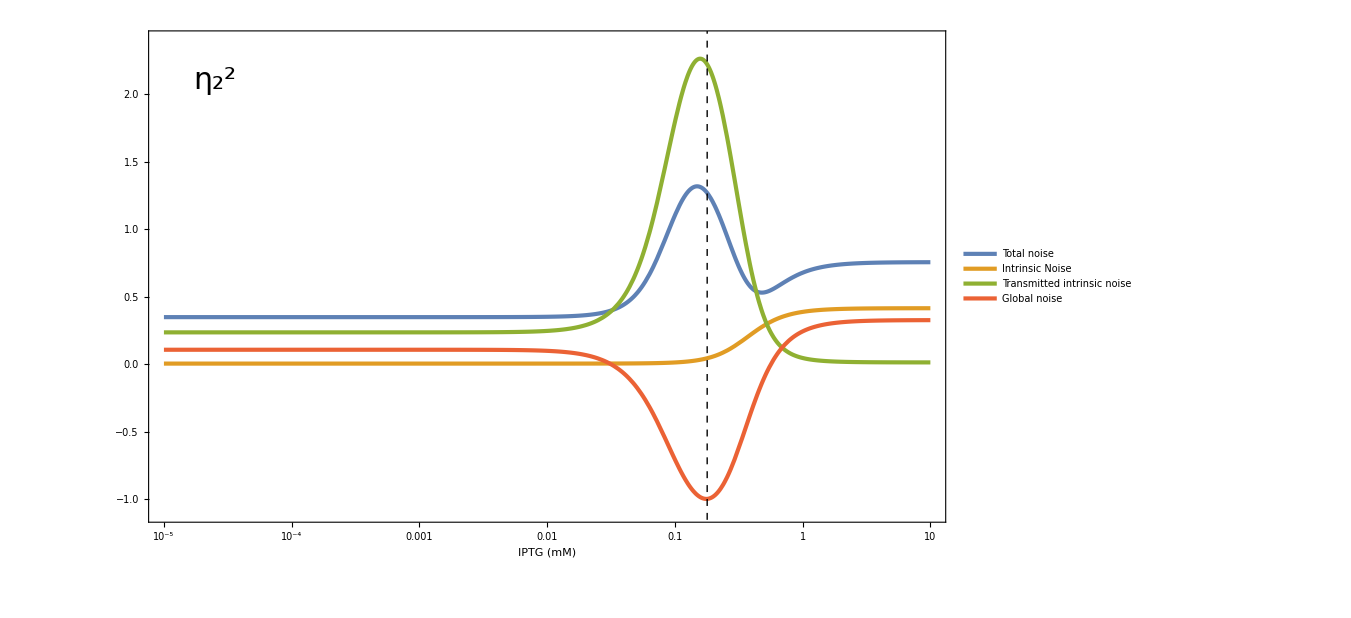

```mathematica
options3 = {Frame->True,PlotRange->{{10^-5,10},{-1.1,2.4}},PlotStyle->AbsoluteThickness[3],FrameStyle->Directive[Black,Thick],LabelStyle->Directive[30,FontFamily->"Palatino Linotype",Black],TicksStyle->Directive[Black,Bold],PlotLegends->Placed[LineLegend[{"Total noise","Intrinsic Noise","Transmitted\nintrinsic noise","Global noise"},LegendMarkerSize->{30},LabelStyle->{FontFamily->"Palatino Linotype",20},LegendLayout->{"Row",4},Spacings->0.2],{0.88,0.82}],FrameLabel->{Text[Style["IPTG (mM)"]],None}};
Show[LogLinearPlot[{eta22[IPTG],eta2int2[IPTG],1/2*(H21[IPTG])^2*eta21[IPTG]+1/8*(H21[IPTG])^2*(H10[IPTG])^2*eta20,etaG^2*(1-H21[IPTG]-1/4*(H21[IPTG])^2*H10[IPTG]+1/2*H21[IPTG]*H10[IPTG])},{IPTG,10^-5,10},Evaluate[options3]],Graphics[Text[Style[ToExpression["\\eta_2^2",TeXForm,HoldForm],30,Black,FontFamily->"Palatino Linotype"],{-10.6,2.1}]],ImageSize->1000,Epilog->{Directive[Black,Dashed,Thick],Line[{{Log[0.178956],5},{Log[0.178959],-2}}]}]
```

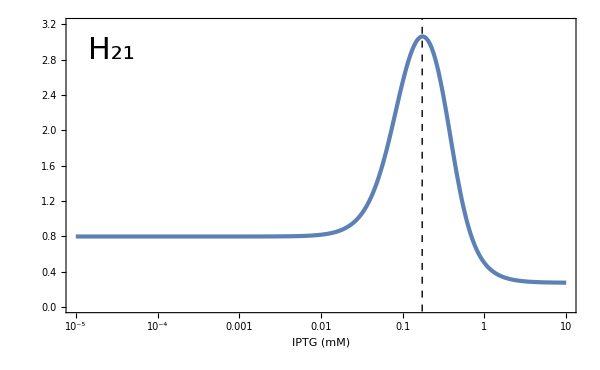

Line[{0.178956,5},{0.178959,-1}]

```mathematica
options4 = {Frame->True,PlotRange->{{10^-5,10},{0,3.2}},PlotStyle->AbsoluteThickness[3],FrameStyle->Directive[Black,Thick],LabelStyle->Directive[25,FontFamily->"Palatino Linotype",Black],TicksStyle->Directive[Black,Bold],FrameLabel->{Text[Style["IPTG (mM)"]],None},Epilog->{Directive[Black,Dashed,Thick],Line[{{Log[0.173],5},{Log[0.173],-1}}]}};
Show[LogLinearPlot[H21[IPTG],{IPTG,10^-5,10},Evaluate[options4]],Graphics[Text[Style[ToExpression["H_{21}",TeXForm,HoldForm],30,Black,FontFamily->"Palatino Linotype"],{-10.5,2.9}]],ImageSize->600]
```